```mathematica
Needs["PlotLegends`"]
```

```mathematica
ν=1/1.6055028269228382;
scpmaxdUdk=Table[{pmaxdUdk[[All,1]][[i]]^(-1/ν),pmaxdUdk[[All,2]][[i]]},{i,1,Length[pmaxdUdk]}]
scpmaxdlnM2dk2=Table[{pmaxdlnM2dk2[[All,1]][[i]]^(-1/ν),pmaxdlnM2dk2[[All,2]][[i]]},{i,1,Length[pmaxdlnM2dk2]}]
scpmaxdlnabsMdk2=Table[{pmaxdlnabsMdk2[[All,1]][[i]]^(-1/ν),pmaxdlnabsMdk2[[All,2]][[i]]},{i,1,Length[pmaxdlnabsMdk2]}]
scpmaxχ=Table[{pmaxχ[[All,1]][[i]]^(-1/ν),pmaxχ[[All,2]][[i]]},{i,1,Length[pmaxχ]}]
scpmaxdcdk=Table[{pmaxdcdk[[All,1]][[i]]^(-1/ν),pmaxdcdk[[All,2]][[i]]},{i,1,Length[pmaxdcdk]}]
scpmaxdabsMdk=Table[{pmaxdabsMdk[[All,1]][[i]]^(-1/ν),pmaxdabsMdk[[All,2]][[i]]},{i,1,Length[pmaxdabsMdk]}]
```

{{0.0354884,0.22077},{0.0185085,0.22077},{0.0116622,0.22077},{0.00608229,0.22101},{0.00383246,0.22125},{0.00199877,0.22147},{0.00125943,0.22153}}

{{0.0354884,0.22077},{0.0185085,0.22077},{0.0116622,0.22097},{0.00608229,0.22133},{0.00383246,0.22147},{0.00199877,0.22157},{0.00125943,0.22159}}

{{0.0354884,0.22077},{0.0185085,0.22091},{0.0116622,0.22125},{0.00608229,0.22147},{0.00383246,0.22155},{0.00199877,0.22161},{0.00125943,0.22163}}

{{0.0354884,0.22223},{0.0185085,0.22223},{0.0116622,0.22205},{0.00608229,0.22189},{0.00383246,0.22181},{0.00199877,0.22175},{0.00125943,0.22171}}

{{0.0354884,0.22077},{0.0185085,0.22111},{0.0116622,0.22135},{0.00608229,0.22153},{0.00383246,0.22161},{0.00199877,0.22163},{0.00125943,0.22163}}

{{0.0354884,0.22321},{0.0185085,0.22321},{0.0116622,0.22313},{0.00608229,0.22249},{0.00383246,0.22221},{0.00199877,0.22195},{0.00125943,0.22183}}

```mathematica
pmaxdUdk
pmaxdlnM2dk2
pmaxdlnabsMdk2
pmaxχ
pmaxdcdk
pmaxdabsMdk
```

{{8,0.22077},{12,0.22077},{16,0.22077},{24,0.22101},{32,0.22125},{48,0.22147},{64,0.22153}}

{{8,0.22077},{12,0.22077},{16,0.22097},{24,0.22133},{32,0.22147},{48,0.22157},{64,0.22159}}

{{8,0.22077},{12,0.22091},{16,0.22125},{24,0.22147},{32,0.22155},{48,0.22161},{64,0.22163}}

{{8,0.22223},{12,0.22223},{16,0.22205},{24,0.22189},{32,0.22181},{48,0.22175},{64,0.22171}}

{{8,0.22077},{12,0.22111},{16,0.22135},{24,0.22153},{32,0.22161},{48,0.22163},{64,0.22163}}

{{8,0.22321},{12,0.22321},{16,0.22313},{24,0.22249},{32,0.22221},{48,0.22195},{64,0.22183}}

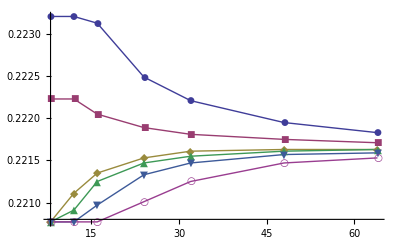

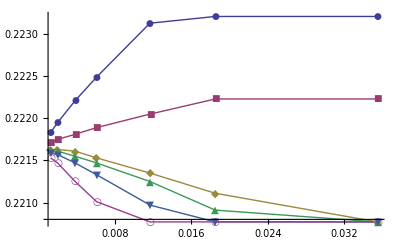

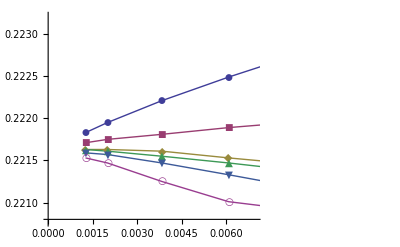

```mathematica
ListPlot[{pmaxdabsMdk,pmaxχ,pmaxdcdk,pmaxdlnabsMdk2,pmaxdlnM2dk2,pmaxdUdk},Joined->True,PlotMarkers->Automatic,PlotRange->Full,PlotLegend->{"|M|","χ","c","ln|M|","lnM^2","U"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{scpmaxdabsMdk,scpmaxχ,scpmaxdcdk,scpmaxdlnabsMdk2,scpmaxdlnM2dk2,scpmaxdUdk},Joined->True,PlotMarkers->Automatic,PlotRange->Full,PlotLegend->{"|M|","χ","c","ln|M|","lnM^2","U"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{scpmaxdabsMdk,scpmaxχ,scpmaxdcdk,scpmaxdlnabsMdk2,scpmaxdlnM2dk2,scpmaxdUdk},Joined->True,PlotMarkers->Automatic,PlotRange->{{0,0.007},Full},PlotLegend->{"|M|","χ","c","ln|M|","lnM^2","U"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{scpmaxdUdk,scpmaxdlnM2dk2,scpmaxdlnabsMdk2,scpmaxχ,scpmaxdcdk,scpmaxdabsMdk},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
ListPlot[{scpmaxdUdk,scpmaxdlnM2dk2,scpmaxdlnabsMdk2,scpmaxχ,scpmaxdcdk,scpmaxdabsMdk},Joined->True,PlotMarkers->Automatic,PlotRange->{{0,0.007},Full}]
```

```mathematica
ListPlot[{pmaxdabsMdk,pmaxχ,pmaxdcdk,pmaxdlnabsMdk2,pmaxdlnM2dk2,pmaxdUdk},Joined->True,PlotMarkers->Automatic,PlotRange->Full,PlotLegend->{"|M|","χ","C","ln|M|","lnM^2","U"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{scpmaxdabsMdk,scpmaxχ,scpmaxdcdk,scpmaxdlnabsMdk2,scpmaxdlnM2dk2,scpmaxdUdk},Joined->True,PlotMarkers->Automatic,PlotRange->Full,PlotLegend->{"|M|","χ","C","ln|M|","lnM^2","U"},LegendPosition->{1.1,-0.4},LegendShadow->None]
ListPlot[{scpmaxdabsMdk,scpmaxχ,scpmaxdcdk,scpmaxdlnabsMdk2,scpmaxdlnM2dk2,scpmaxdUdk},Joined->True,PlotMarkers->Automatic,PlotRange->{{0,0.007},Full},PlotLegend->{"|M|","χ","C","ln|M|","lnM^2","U"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Do[
For[k=0.22225,k<0.22325,k += 0.00002,
z[k][l]=Sum[his[l][[All,2]][[i]]*Exp[(k0-k)*his[l][[All,1]][[i]]],{i,1,Length[his[l]]}];
hist[k][l]=Table[{his[l][[All,1]][[i]],his[l][[All,2]][[i]]*Exp[(k0-k)*his[l][[All,1]][[i]]]/z[k][l]},{i,1,Length[his[l]]}];
absM[l]=Append[absM[l],{k,Sum[hist[k][l][[All,2]][[i]]*am[l][[i]],{i,1,Length[hist[k][l]]}]}]
]
,{l,{8,12,16,24,32,48,64,96}}]
```

```mathematica
Do[
dabsMdk[l]=Table[{absM[l][[All,1]][[i]],(absM[l][[All,2]][[i+1]]-absM[l][[All,2]][[i-1]])/(absM[l][[All,1]][[i+1]]-absM[l][[All,1]][[i-1]])},{i,2,Length[absM[l]]-1}]

,{l,{8,12,16,24,32,48,64,96}}]
```

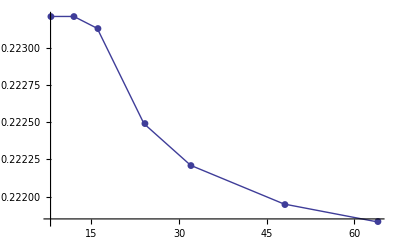

```mathematica
ListPlot[{pmaxdabsMdk},Joined->True,PlotMarkers->Automatic,PlotRange->Full]
```

```mathematica
pmaxdabsMdk
```

{{8,0.22321},{12,0.22321},{16,0.22313},{24,0.22249},{32,0.22221},{48,0.22195},{64,0.22183}}

```mathematica
pmaxdUdk
pmaxdlnM2dk2
pmaxdlnabsMdk2
pmaxχ
pmaxdcdk
pmaxdabsMdk
```

```mathematica
pmaxdUdk1={{24,0.2210099999999999},{32,0.2212499999999998},{48,0.22146999999999972},{64,0.2215299999999997}}
pmaxdlnM2dk1={{24,0.22132999999999978},{32,0.22146999999999972},{48,0.22156999999999968},{64,0.22158999999999968}}
pmaxdlnabsMdk1={{24,0.22146999999999972},{32,0.2215499999999997},{48,0.22160999999999967},{64,0.22162999999999966}}
pmaxχ1={{24,0.22188999999999956},{32,0.2218099999999996},{48,0.22174999999999961},{64,0.22170999999999963}}
pmaxdcdk1={{16,0.22134999999999977},{24,0.2215299999999997},{32,0.22160999999999967},{48,0.22162999999999966},{64,0.22162999999999966}}
pmaxdabsMdk1={{24,0.2224899999999999},{32,0.22220999999999944},{48,0.22194999999999954},{64,0.22182999999999958}}
```

{{24,0.22101},{32,0.22125},{48,0.22147},{64,0.22153}}

{{24,0.22133},{32,0.22147},{48,0.22157},{64,0.22159}}

{{24,0.22147},{32,0.22155},{48,0.22161},{64,0.22163}}

{{24,0.22189},{32,0.22181},{48,0.22175},{64,0.22171}}

{{16,0.22135},{24,0.22153},{32,0.22161},{48,0.22163},{64,0.22163}}

{{24,0.22249},{32,0.22221},{48,0.22195},{64,0.22183}}

```mathematica
model=d0+c0*x^(-1/ν)+c1*x^a


nlf=NonlinearModelFit[pmaxdabsMdk1,model,{d0,c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxχ1,model,{d0,c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdcdk1,model,{d0,c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdlnabsMdk1,model,{d0,c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdlnM2dk1,model,{d0,c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdUdk1,model,{d0,c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

model=d0+c0*x^(-a)

nlf=NonlinearModelFit[pmaxdabsMdk1,model,{d0,c0,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxχ1,model,{d0,c0,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdcdk1,model,{d0,c0,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdlnabsMdk1,model,{d0,c0,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdlnM2dk1,model,{d0,c0,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdUdk1,model,{d0,c0,a},x];

nlf[{"BestFit","ParameterTable"}]

model=d0+a0*x^(-1/ν)*(1+b0*x^(-1/(2*ν))+c0*x^(-1/ν))

nlf=NonlinearModelFit[pmaxdabsMdk1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxχ1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdcdk1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdlnabsMdk1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdlnM2dk1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdUdk1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]


model=d0+a0*x^(-1/ν)*(1+b0*x^c0)

nlf=NonlinearModelFit[pmaxdabsMdk1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxχ1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdcdk1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdlnabsMdk1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdlnM2dk1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdUdk1,model,{d0,c0,a0,b0},x];

nlf[{"BestFit","ParameterTable"}]
```

d0+c0/x^1.6055+c1 x^a

{0.222698+0.108287/x^1.6055-0.000534171 x^0.152067,Missing[]}

{0.221704+0.0315082/x^1.6055-5.89051×10^-8 x^1.51654,Missing[]}

{0.221809-0.036563/x^1.6055-2.15479×10^-6 x^0.994405, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221809 | 0.00031067 | 713.97 | 0.000891662
c0 | -0.036563 | 0.00990482 | -3.69144 | 0.168416
c1 | -2.15479×10^-6 | 0.0000288178 | -0.0747727 | 0.952487
a | 0.994405 | 2.69394 | 0.369127 | 0.774884}

{0.221768-0.0385218/x^1.6055-0.0000211099 x^0.347046,Missing[]}

{0.22188-0.0722549/x^1.6055-0.0000168272 x^0.59251,Missing[]}

{0.2217-0.113728/x^1.6055-5.05008×10^-10 x^2.58442,Missing[]}

d0+c0 x^-a

{0.221545+0.0458316/x^1.2212, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221545 | 8.41127×10^-7 | 263390. | 2.41702×10^-6
c0 | 0.0458316 | 0.000238353 | 192.284 | 0.0033108
a | 1.2212 | 0.00189262 | 645.244 | 0.000986633}

{0.221638+0.0126477/x^1.23366, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221638 | 0.0000495874 | 4469.65 | 0.000142432
c0 | 0.0126477 | 0.0148835 | 0.849779 | 0.551587
a | 1.23366 | 0.427128 | 2.88828 | 0.212192}

{0.221646-0.367419/x^2.56809, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221646 | 0.0000151681 | 14612.6 | 4.68324×10^-9
c0 | -0.367419 | 0.450959 | -0.814751 | 0.500802
a | 2.56809 | 0.452965 | 5.66951 | 0.0297302}

{0.221659-0.0873766/x^1.93088, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221659 | 2.76025×10^-6 | 80303.8 | 7.92764×10^-6
c0 | -0.0873766 | 0.0168287 | -5.19211 | 0.12113
a | 1.93088 | 0.0643331 | 30.0138 | 0.0212031}

{0.221623-0.482327/x^2.32952, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221623 | 0.0000147836 | 14991.2 | 0.0000424663
c0 | -0.482327 | 0.44813 | -1.07631 | 0.476613
a | 2.32952 | 0.30416 | 7.65888 | 0.0826542}

{0.221666-0.129542/x^1.66226, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221666 | 0.0000628708 | 3525.73 | 0.000180564
c0 | -0.129542 | 0.124907 | -1.03711 | 0.488403
a | 1.66226 | 0.32907 | 5.0514 | 0.12442}

d0+(a0 (1+c0/x^1.6055+b0/x^0.802751))/x^1.6055

{0.221582+(0.25987 (1+31.6278/x^1.6055-7.92028/x^0.802751))/x^1.6055,Missing[]}

{0.221563+(0.254082 (1+121.229/x^1.6055-19.5666/x^0.802751))/x^1.6055,Missing[]}

{0.221558+(0.141666 (1+92.9886/x^1.6055-20.4681/x^0.802751))/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221558 | 0.0000315217 | 7028.75 | 0.0000905737
c0 | 92.9886 | 4.4083 | 21.094 | 0.0301576
a0 | 0.141666 | 0.0490967 | 2.88544 | 0.212385
b0 | -20.4681 | 0.675452 | -30.3028 | 0.021001}

{0.221649+(0.00909868 (1+478.052/x^1.6055-91.5492/x^0.802751))/x^1.6055,Missing[]}

{0.221541+(0.176685 (1+155.826/x^1.6055-27.4915/x^0.802751))/x^1.6055,Missing[]}

{0.221477+(0.320286 (1+201.689/x^1.6055-31.6249/x^0.802751))/x^1.6055,Missing[]}

d0+(a0 (1+b0 x^c0))/x^1.6055

{0.221533+(0.0289215 (1+0.949705 x^0.485256))/x^1.6055,Missing[]}

{0.221648+(0.298601 (1-1.01204/x^0.0485315))/x^1.6055,Missing[]}

{0.220904-(0.043936 (1-0.0325637 x^1.46052))/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.220904 | 0.0169856 | 13.0054 | 0.0488544
c0 | 1.46052 | 3.12999 | 0.46662 | 0.722059
a0 | -0.043936 | 0.0381057 | -1.153 | 0.454835
b0 | -0.0325637 | 0.308358 | -0.105604 | 0.933019}

{0.221659-(0.00580405 (1+15.2821/x^0.393984))/x^1.6055,Missing[]}

{0.221469-(0.0929023 (1-0.0293718 x^1.02045))/x^1.6055,Missing[]}

{0.22142-(0.116665 (1-0.00378346 x^1.48072))/x^1.6055,Missing[]}

```mathematica
----------------------------------------------------------------------------------------------------------------
```

```mathematica
model=d0+c0*x^(-1/ν)


nlf1=NonlinearModelFit[pmaxdabsMdk1,model,{d0,c0},x];

nlf1[{"BestFit","ParameterTable"}]

nlf2=NonlinearModelFit[pmaxχ1,model,{d0,c0},x];

nlf2[{"BestFit","ParameterTable"}]

nlf3=NonlinearModelFit[pmaxdcdk1,model,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]

nlf4=NonlinearModelFit[pmaxdlnabsMdk1,model,{d0,c0},x];

nlf4[{"BestFit","ParameterTable"}]

nlf5=NonlinearModelFit[pmaxdlnM2dk1,model,{d0,c0},x];

nlf5[{"BestFit","ParameterTable"}]

nlf6=NonlinearModelFit[pmaxdUdk1,model,{d0,c0},x];

nlf6[{"BestFit","ParameterTable"}]
```

d0+c0/x^1.6055

{0.221672+0.136176/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221672 | 0.0000172966 | 12815.9 | 6.08838×10^-9
c0 | 0.136176 | 0.00457144 | 29.7885 | 0.00112505}

{0.22167+0.0363195/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.22167 | 6.76185×10^-6 | 32782.5 | 9.30497×10^-10
c0 | 0.0363195 | 0.00178714 | 20.3228 | 0.00241246}

{0.221689-0.0280845/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221689 | 0.000017472 | 12688.2 | 1.07961×10^-12
c0 | -0.0280845 | 0.00281025 | -9.99357 | 0.00213241}

{0.221675-0.0333893/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221675 | 3.52957×10^-6 | 62805.1 | 2.53519×10^-10
c0 | -0.0333893 | 0.000932855 | -35.7926 | 0.000779659}

{0.221671-0.0550348/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221671 | 0.0000135296 | 16384.2 | 3.72522×10^-9
c0 | -0.0550348 | 0.00357584 | -15.3908 | 0.00419508}

{0.221676-0.109758/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221676 | 0.0000117935 | 18796.5 | 2.83039×10^-9
c0 | -0.109758 | 0.00311698 | -35.213 | 0.000805506}

```mathematica
f1[x_]=nlf1["ParameterTableEntries"][[1]][[1]]+nlf1["ParameterTableEntries"][[2]][[1]]*x;
f2[x_]=nlf2["ParameterTableEntries"][[1]][[1]]+nlf2["ParameterTableEntries"][[2]][[1]]*x;
f3[x_]=nlf3["ParameterTableEntries"][[1]][[1]]+nlf3["ParameterTableEntries"][[2]][[1]]*x;
f4[x_]=nlf4["ParameterTableEntries"][[1]][[1]]+nlf4["ParameterTableEntries"][[2]][[1]]*x;
f5[x_]=nlf5["ParameterTableEntries"][[1]][[1]]+nlf5["ParameterTableEntries"][[2]][[1]]*x;
f6[x_]=nlf6["ParameterTableEntries"][[1]][[1]]+nlf6["ParameterTableEntries"][[2]][[1]]*x;
```

```mathematica
f4[x]
```

0.221675+3.52957×10^-6 x

```mathematica
PlotLegend->{"|M|","χ","C","ln|M|","lnM^2","U"},LegendPosition->{1.1,-0.4},LegendShadow->None
```

-Graphics-

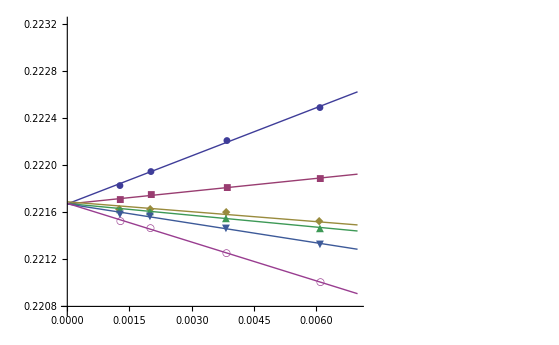

```mathematica
ListPlot[{scpmaxdabsMdk,scpmaxχ,scpmaxdcdk,scpmaxdlnabsMdk2,scpmaxdlnM2dk2,scpmaxdUdk},Joined->True,PlotMarkers->Automatic,PlotRange->{{0,0.007},Full},PlotLegend->{"|M|","χ","C","ln|M|","lnM^2","U"},LegendPosition->{1.1,-0.4},LegendShadow->None]
pic1=Plot[{f1[x],f2[x],f3[x],f4[x],f5[x],f6[x]},{x,0,0.007}];
pic2=ListPlot[{scpmaxdabsMdk,scpmaxχ,scpmaxdcdk,scpmaxdlnabsMdk2,scpmaxdlnM2dk2,scpmaxdUdk},PlotMarkers->Automatic,PlotRange->{{0,0.007},Full}];
Show[{pic2,pic1}]
```

```mathematica
----------------------------------------------------------------------------------------------------------------
```

```mathematica
model=d0+c0*x^(-a0)


nlf1=NonlinearModelFit[pmaxdabsMdk1,model,{d0,c0,a0},x];

nlf1[{"BestFit","ParameterTable"}]

nlf2=NonlinearModelFit[pmaxχ1,model,{d0,c0,a0},x];

nlf2[{"BestFit","ParameterTable"}]

nlf3=NonlinearModelFit[pmaxdcdk1,model,{d0,c0,a0},x];

nlf3[{"BestFit","ParameterTable"}]

nlf4=NonlinearModelFit[pmaxdlnabsMdk1,model,{d0,c0,a0},x];

nlf4[{"BestFit","ParameterTable"}]

nlf5=NonlinearModelFit[pmaxdlnM2dk1,model,{d0,c0,a0},x];

nlf5[{"BestFit","ParameterTable"}]

nlf6=NonlinearModelFit[pmaxdUdk1,model,{d0,c0,a0},x];

nlf6[{"BestFit","ParameterTable"}]
```

d0+c0 x^-a0

{0.221545+0.0458316/x^1.2212, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221545 | 8.41127×10^-7 | 263390. | 2.41702×10^-6
c0 | 0.0458316 | 0.000238353 | 192.284 | 0.0033108
a0 | 1.2212 | 0.00189262 | 645.244 | 0.000986633}

{0.221638+0.0126477/x^1.23366, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221638 | 0.0000495874 | 4469.65 | 0.000142432
c0 | 0.0126477 | 0.0148835 | 0.849779 | 0.551587
a0 | 1.23366 | 0.427128 | 2.88828 | 0.212192}

{0.221646-0.367419/x^2.56809, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221646 | 0.0000151681 | 14612.6 | 4.68324×10^-9
c0 | -0.367419 | 0.450959 | -0.814751 | 0.500802
a0 | 2.56809 | 0.452965 | 5.66951 | 0.0297302}

{0.221659-0.0873766/x^1.93088, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221659 | 2.76025×10^-6 | 80303.8 | 7.92764×10^-6
c0 | -0.0873766 | 0.0168287 | -5.19211 | 0.12113
a0 | 1.93088 | 0.0643331 | 30.0138 | 0.0212031}

{0.221623-0.482327/x^2.32952, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221623 | 0.0000147836 | 14991.2 | 0.0000424663
c0 | -0.482327 | 0.44813 | -1.07631 | 0.476613
a0 | 2.32952 | 0.30416 | 7.65888 | 0.0826542}

{0.221666-0.129542/x^1.66226, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.221666 | 0.0000628708 | 3525.73 | 0.000180564
c0 | -0.129542 | 0.124907 | -1.03711 | 0.488403
a0 | 1.66226 | 0.32907 | 5.0514 | 0.12442}

```mathematica
scpmaxdabsMdk2=Table[{pmaxdabsMdk[[All,1]][[i]]^(-nlf1["ParameterTableEntries"][[3]][[1]]),pmaxdabsMdk[[All,2]][[i]]},{i,1,Length[pmaxdabsMdk]}]
scpmaxχ2=Table[{pmaxχ[[All,1]][[i]]^(-nlf2["ParameterTableEntries"][[3]][[1]]),pmaxχ[[All,2]][[i]]},{i,1,Length[pmaxχ]}]
scpmaxdcdk2=Table[{pmaxdcdk[[All,1]][[i]]^(-nlf3["ParameterTableEntries"][[3]][[1]]),pmaxdcdk[[All,2]][[i]]},{i,1,Length[pmaxdcdk]}]
scpmaxdlnabsMdk22=Table[{pmaxdlnabsMdk2[[All,1]][[i]]^(-nlf4["ParameterTableEntries"][[3]][[1]]),pmaxdlnabsMdk2[[All,2]][[i]]},{i,1,Length[pmaxdlnabsMdk2]}]
scpmaxdlnM2dk22=Table[{pmaxdlnM2dk2[[All,1]][[i]]^(-nlf5["ParameterTableEntries"][[3]][[1]]),pmaxdlnM2dk2[[All,2]][[i]]},{i,1,Length[pmaxdlnM2dk2]}]
scpmaxdUdk2=Table[{pmaxdUdk[[All,1]][[i]]^(-nlf6["ParameterTableEntries"][[3]][[1]]),pmaxdUdk[[All,2]][[i]]},{i,1,Length[pmaxdUdk]}]
```

```mathematica
f1[x_]=nlf1["ParameterTableEntries"][[1]][[1]]+nlf1["ParameterTableEntries"][[2]][[1]]*x;
f2[x_]=nlf2["ParameterTableEntries"][[1]][[1]]+nlf2["ParameterTableEntries"][[2]][[1]]*x;
f3[x_]=nlf3["ParameterTableEntries"][[1]][[1]]+nlf3["ParameterTableEntries"][[2]][[1]]*x;
f4[x_]=nlf4["ParameterTableEntries"][[1]][[1]]+nlf4["ParameterTableEntries"][[2]][[1]]*x;
f5[x_]=nlf5["ParameterTableEntries"][[1]][[1]]+nlf5["ParameterTableEntries"][[2]][[1]]*x;
f6[x_]=nlf6["ParameterTableEntries"][[1]][[1]]+nlf6["ParameterTableEntries"][[2]][[1]]*x;
```

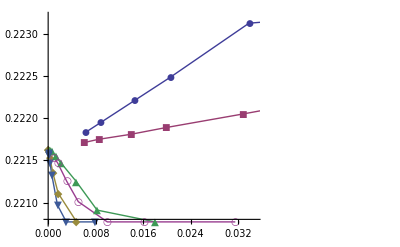

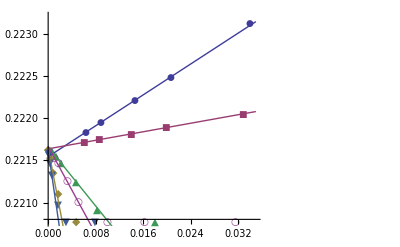

```mathematica
ListPlot[{scpmaxdabsMdk2,scpmaxχ2,scpmaxdcdk2,scpmaxdlnabsMdk22,scpmaxdlnM2dk22,scpmaxdUdk2},Joined->True,PlotMarkers->Automatic,PlotRange->{{0,0.035},Full},PlotLegend->{"|M|","χ","C","ln|M|","lnM^2","U"},LegendPosition->{1.1,-0.4},LegendShadow->None]
pic1=Plot[{f1[x],f2[x],f3[x],f4[x],f5[x],f6[x]},{x,0,0.035}];
pic2=ListPlot[{scpmaxdabsMdk2,scpmaxχ2,scpmaxdcdk2,scpmaxdlnabsMdk22,scpmaxdlnM2dk22,scpmaxdUdk2},PlotMarkers->Automatic,PlotRange->{{0,0.035},Full}];
Show[{pic2,pic1}]
```

```mathematica
model=0.22167+x^(-1/ν)*(c0+c1*x^a)


nlf=NonlinearModelFit[pmaxdabsMdk1,model,{c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxχ1,model,{c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdcdk1,model,{c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdlnabsMdk1,model,{c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdlnM2dk1,model,{c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]

nlf=NonlinearModelFit[pmaxdUdk1,model,{c0,c1,a},x];

nlf[{"BestFit","ParameterTable"}]
```

0.22167+(c0+c1 x^a)/x^1.6055

{0.22167+(-0.597231+0.720634 x^0.00542321)/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
c0 | -0.597231 | 2887.4 | -0.000206841 | 0.999868
c1 | 0.720634 | 2886.87 | 0.000249624 | 0.999841
a | 0.00542321 | 21.3157 | 0.000254423 | 0.999838}

{0.22167+(-0.193848+0.227061 x^0.00420048)/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
c0 | -0.193848 | 1937.77 | -0.000100037 | 0.999936
c1 | 0.227061 | 1937.55 | 0.000117189 | 0.999925
a | 0.00420048 | 35.3176 | 0.000118934 | 0.999924}

{0.22167+(-0.803453+0.750567 x^0.0121596)/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
c0 | -0.803453 | 187.674 | -0.00428111 | 0.996973
c1 | 0.750567 | 187.538 | 0.00400222 | 0.99717
a | 0.0121596 | 2.92443 | 0.00415793 | 0.99706}

{0.22167+(-0.163112+0.120662 x^0.0243711)/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
c0 | -0.163112 | 22.4467 | -0.00726664 | 0.995374
c1 | 0.120662 | 22.3682 | 0.00539436 | 0.996566
a | 0.0243711 | 4.15842 | 0.00586067 | 0.996269}

{0.22167+(-0.613843+0.549164 x^0.00538322)/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
c0 | -0.613843 | 2300.23 | -0.000266862 | 0.99983
c1 | 0.549164 | 2299.82 | 0.000238786 | 0.999848
a | 0.00538322 | 22.1219 | 0.000243343 | 0.999845}

{0.22167+(-0.12308+0.0066435 x^0.240361)/x^1.6055, | Estimate | Standard Error | t-Statistic | P-Value
c0 | -0.12308 | 1.01163 | -0.121666 | 0.922924
c1 | 0.0066435 | 0.799571 | 0.00830883 | 0.994711
a | 0.240361 | 15.5747 | 0.0154328 | 0.990176}